```mathematica
coordinates={ρ Sin[ω t],ρ Cos[ω t],γ  t}
```

{ρ sin(t ω),ρ cos(t ω),γ t}

```mathematica
velocity= D[coordinates, t]
```

{ρ ω cos(t ω),-ρ ω sin(t ω),γ}

```mathematica
Simplify[√(velocity.velocity)]
```

√(γ^2+ρ^2 ω^2)

```mathematica
acceleration = D[D[coordinates, t], t]
```

{-ρ ω^2 sin(t ω),-ρ ω^2 cos(t ω),0}

```mathematica
PowerExpand[Simplify[√(acceleration.acceleration)]]
```

ρ ω^2

```mathematica
parameterRules= {ρ -> 1, ω->1/2,γ->1/10}
```

{ρ→1,ω→1/2,γ→1/10}

```mathematica
Coord=coordinates/.parameterRules
```

{sin(t/2),cos(t/2),t/10}

```mathematica
vel=velocity /.parameterRules
```

{1/2 cos(t/2),-1/2 sin(t/2),1/10}

```mathematica
accel=acceleration /.parameterRules
```

{-1/4 sin(t/2),-1/4 cos(t/2),0}

```mathematica
track=ParametricPlot3D[Coord,{t,0,10π}]
```

-Graphics3D-

```mathematica
points=Table[{RGBColor[0,0,0.996109],PointSize[.03],Point[Coord]},{t,0,10π,.5}];
Show[Graphics3D[points]]
```

-Graphics3D-

```mathematica
li=Table[{RGBColor[0.996109,0,0],Arrow[{Coord,Coord+vel * 1.5}]},{t,0,10π,.5}];
Show[Graphics3D[li]]
```

-Graphics3D-

```mathematica
ac=Table[{RGBColor[0,0.500008,0],Arrow[{Coord,accel *1.5+Coord}]},{t,0,10π,.5}];
Show[Graphics3D[ac]]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{li,ac,points}]]
```

-Graphics3D-

```mathematica
all = Transpose[{li,ac,points}];
Show[Graphics3D[all]]
```

-Graphics3D-

```mathematica
ListAnimate[(Show[Graphics3D[#1], track, PlotRange -> {{-1.5, 1.5}, {-1.5, 1.5}, {-0.1, 3.0}}] &) /@ all]
```

```mathematica
velocity.acceleration
```

0

```mathematica
track={t vx+x0,1/2(-g) t^2+vy t+y0}
```

{t vx+x0,-(g t^2)/2+t vy+y0}

```mathematica
cond1=Solve[Thread[{0,0}==track /.t ->  0,List],{x0,y0}] //Flatten
```

{x0→0,y0→0}

```mathematica
tracS=track /.cond1
```

{t vx,t vy-(g t^2)/2}

```mathematica
cond2=Flatten[
Solve[Thread[{v Cos[α],v Sin[α]}==D[tracS, t] /.t -> 0,List],{vx,vy}]]
```

{vx→v cos(α),vy→v sin(α)}

```mathematica
tracS1=tracS /.cond2
```

{t v cos(α),t v sin(α)-(g t^2)/2}

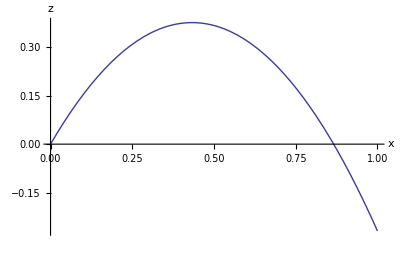

```mathematica
BallTrack=ParametricPlot[Evaluate[tracS1 /.{v ->  1,α-> π/3,g->1}],{t,0,2},AxesLabel -> {"x","z"}]
```

```mathematica
Ball=Table[{RGBColor[0,0,0.62501],PointSize[.08],Point[tracS1 /.{v ->  1,α-> π/3,g->1}]},{t,0,1.8,.1}];
```

```mathematica
ListAnimate[(Show[BallTrack,Graphics[#1],PlotRange->{-0.2,0.5}]&) /@ Ball]
```

## FeynCalc

### Tools and Tables for Quantum Field Theory Calculations

http://www.feyncalc.org/

To install the latest version of FeynCalc (still fc820), run the following instruction in a Kernel or Notebook session of Mathematica 7, 8 or 9 on Linux, MacOSX, or Windows.
Import[“http://www.feyncalc.org/install.m”]

```mathematica
Import["http://www.feyncalc.org/install.m"]
```

downloading http://www.feyncalc.org/download/fclatest.zip   please wait

Downloading done, installing FeynCalc to C:\Users\Administrator\AppData\Roaming\Mathematica\Applications

installation of FeynCalc ready.

loading FeynCalc

Loading FeynCalc from C:\Users\Administrator\AppData\Roaming\Mathematica\Applications\HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

```mathematica
<<HighEnergyPhysics`FeynCalc`
```

Loading FeynCalc from C:\Users\Administrator\AppData\Roaming\Mathematica\Applications\HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

```mathematica
<<HighEnergyPhysics`fc`
```

```mathematica
?FeynCalc
```

For installation notes visit www.feyncalc.org

For a list of availabe objects type $FeynCalcStuff, which contains a list of all functions and options in StringForm. You can get on-line information by ?function, e.g. ?Contract.

There are several useful functions for short input, type $FCS for a list of short commands. Then type, e.g., ?GA.


To enable/disable start-up messages, put the line

$FeynCalcStartupMessages = True;

or

$FeynCalcStartupMessages = False;

 into your "init.m" file or into your "FCConfig.m" file.

```mathematica
p1/: MakeBoxes[p1, fmt_] := InterpretationBox[SubscriptBox[p, 1], p1]
```

```mathematica
k1/: MakeBoxes[k1, fmt_] := InterpretationBox[SubscriptBox[k, 1], k1]
```

```mathematica
p2/: MakeBoxes[p2, fmt_] := InterpretationBox[SubscriptBox[p, 2], p2]
```

```mathematica
k2/: MakeBoxes[k2, fmt_] := InterpretationBox[SubscriptBox[k, 2], k2]
```

```mathematica
{p1sl,p2sl,k1sl,k2sl}=DiracSlash/@{p1,p2,k1,k2}
```

{γ·p1,γ·p2,γ·k1,γ·k2}

```mathematica
DiracSlash[x]
```

γ·x

```mathematica
ScalarProduct[p1,p1]=ScalarProduct[p2,p2]=m^2;
```

```mathematica
ScalarProduct[k1,k1]=ScalarProduct[k2,k2]=0;
```

```mathematica
ScalarProduct[k1,k2]=ScalarProduct[p1,p2]+m^2;
```

```mathematica
ScalarProduct[k1,p2]=ScalarProduct[k2,p1];
```

```mathematica
ScalarProduct[k2,p2]=ScalarProduct[k1,p1];
```

```mathematica
ScalarProduct[p1,p2]=ScalarProduct[k2,p1]-m^2+ScalarProduct[k1,p1];
```

```mathematica
f1=DiracMatrix[μ].(p1sl-k1sl+m).DiracMatrix[ν]
```

γ^μ.(-γ·k1+m+γ·p1).γ^ν

```mathematica
f2=DiracMatrix[ν].(p1sl-k2sl+m).DiracMatrix[μ]
```

γ^ν.(-γ·k2+m+γ·p1).γ^μ

```mathematica
f3=DiracMatrix[ν].(p1sl-k1sl+m).DiracMatrix[μ]
```

γ^ν.(-γ·k1+m+γ·p1).γ^μ

```mathematica
f4=DiracMatrix[μ].(p1sl-k2sl+m).DiracMatrix[ν]
```

γ^μ.(-γ·k2+m+γ·p1).γ^ν

```mathematica
tr1 = Tr[(p1sl + m) . f1 . (p2sl - m).f3 ]
```

4 (8 k1·p1 k2·p1+8 m^2 k1·p1-8 m^4)

```mathematica
tr2 = Tr[(p1sl + m) . f1 . (p2sl - m).f4]
```

4 (4 m^2 k1·p1+4 m^2 k2·p1-8 m^4)

```mathematica
tr3 = Tr[(p1sl + m) . f2 . (p2sl - m).f3 ]
```

4 (4 m^2 k1·p1+4 m^2 k2·p1-8 m^4)

```mathematica
tr4 = Tr[(p1sl + m) . f2 . (p2sl - m) . f4]
```

4 (8 k1·p1 k2·p1+8 m^2 k2·p1-8 m^4)

```mathematica
matrixsq=tr1/ScalarProduct[2 p1,k1]^2+tr4/ScalarProduct[2 p1,k2]^2+(tr2+tr3)/(ScalarProduct[2 p1,k1] ScalarProduct[2 p1,k2])
```

(2 (4 m^2 k1·p1+4 m^2 k2·p1-8 m^4))/(k1·p1 k2·p1)+(8 k1·p1 k2·p1+8 m^2 k1·p1-8 m^4)/(k1·p1)^2+(8 k1·p1 k2·p1+8 m^2 k2·p1-8 m^4)/(k2·p1)^2

```mathematica
r=Collect2[matrixsq,m]
```

-(8 m^4 (k1·p1+k2·p1)^2)/((k1·p1)^2 (k2·p1)^2)+(16 m^2 (k1·p1+k2·p1))/(k1·p1 k2·p1)+(8 ((k1·p1)^2+(k2·p1)^2))/(k1·p1 k2·p1)

```mathematica
(r - (r /. { k1:>k2, k2:>k1}))
```

0

```mathematica
SetOptions[FORM2FeynCalc,Replace->{"ln(x)"->"Log[x]","ln(1+x)"->"Log[1+x]","ln(1-x)"->"Log[1-x]","Li2(-x)"->"Li2[-x]","Li2(1-x)"->"Li2[1-x]","Li3(1-x)"->"Li3[1-x]","Li3(-x)"->"Li3[-x]","S12(1-x)"->"Nielsen[1,2,1-x]","S12(-x)"->"Nielsen[1,2,-x]","S12(x^2)"->"Nielsen[1,2,x^2]","Z2"->"Zeta2","Z3"->"Zeta[3]","[1+x]^-1"->"(1+x)^-1","[(1-x)+]^-1"->"(1-x)^-1","[1-x]^-1"->"(1-x)^-1","delta"->"DeltaFunction[1-x]","Ca"->"CA","Cf"->"CF"},Dot->Times,HoldForm->False]
```

{Dimension→4,FinalSubstitutions→{},Dot→Times,HoldForm→False,LorentzIndex→{mu,nu,al,be},Set→False,Replace→{ln(x)→Log[x],ln(1+x)→Log[1+x],ln(1-x)→Log[1-x],Li2(-x)→Li2[-x],Li2(1-x)→Li2[1-x],Li3(1-x)→Li3[1-x],Li3(-x)→Li3[-x],S12(1-x)→Nielsen[1,2,1-x],S12(-x)→Nielsen[1,2,-x],S12(x^2)→Nielsen[1,2,x^2],Z2→Zeta2,Z3→Zeta[3],[1+x]^-1→(1+x)^-1,[(1-x)+]^-1→(1-x)^-1,[1-x]^-1→(1-x)^-1,delta→DeltaFunction[1-x],Ca→CA,Cf→CF},Vectors→Automatic}

```mathematica
Clear[r];
```

```mathematica
equation8=-m g == m D[r[t], t,t]
```

-g m==m r''(t)

```mathematica
solution=DSolve[equation8, r, t]
```

{{r→({t}↦c_2 t+c_1-(g t^2)/2)}}

```mathematica
solution=DSolve[{equation8, r[0]==r0, r'[0]==v0}, r, t]//Flatten
```

{r→({t}↦1/2 (-g t^2+2 r0+2 t v0))}

```mathematica
ssol=r[t]/. solution /. {r0 -> 100, v0 -> 0, g -> 9.81}
```

1/2 (200-9.81 t^2)

```mathematica
end=Solve[ssol ==0, t]
```

{{t→-4.51524},{t→4.51524}}

```mathematica
Tend =t /. end⟦2⟧
```

4.51524

```mathematica
track=Table[{RGBColor[0.996109, 0, 0],
Disk[{0, ssol}, 5]}, {t, 0, Tend, .2}];
```

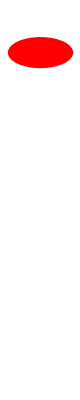
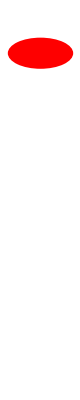
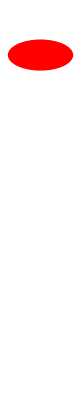
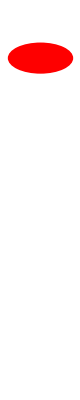
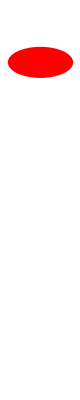
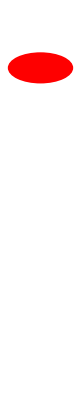
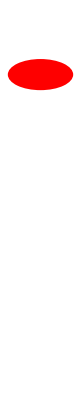
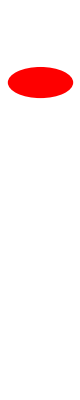

```mathematica
Show[Graphics[#], PlotRange ->
{0, 105},AspectRatio ->Automatic]& /@ track
```

```mathematica
Show[Graphics[#], PlotRange ->
{0, 105},AspectRatio ->Automatic]& /@ track //ListAnimate
```

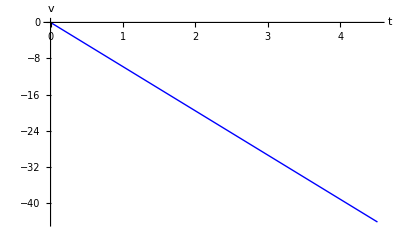

```mathematica
Plot[Evaluate[D[ssol, t]],
{t, 0, Tend}, AxesLabel -> {"t", "v"},
PlotStyle -> RGBColor[0, 0, 0.996109]]
```